# Caltech 101

## Set Environment

```mathematica
home = "/home/lichao/scratch/caltech/";workdir = "/home/lichao/git/geonb/";
```

```mathematica
SetDirectory[workdir];Needs["Posecpp`","posecpp_network.wl"];
```

```mathematica
prefix = "face/";suffix="";
```

## Generate Network 2

### load raw data

```mathematica
rawData=LoadNetwork2Raw[home<>prefix<>"net2_raw"<>suffix<>".txt"];rawData//Dimensions
```

{318806,8}

```mathematica
rawData[[1;;3]]//MatrixForm
```

(0 | 1557 | 7.80339 | 1.56837 | 0.066639 | -0.168281 | -0.128243 | -0.299334
1 | 1200 | 15.5003 | 6.5622 | 0.201504 | 2.37905 | -0.503585 | 0.118121
2 | 2974 | 16.8803 | 5.75198 | 0.151688 | 0.876645 | -0.611957 | 0.0368)

```mathematica
rawData[[1;;3]]//MatrixForm
```

(0 | 1557 | 7.80339 | 1.56837 | 0.066639 | -0.168281 | -0.128243 | -0.299334
1 | 1200 | 15.5003 | 6.5622 | 0.201504 | 2.37905 | -0.503585 | 0.118121
2 | 2974 | 16.8803 | 5.75198 | 0.151688 | 0.876645 | -0.611957 | 0.0368)

### find best threshold

```mathematica
Module[{n = 500,v=2,a},a =ConstructNetwork2[rawData,n,v];Sow[Length[a]];
Complement[a,ConstructNetwork2[rawData,n,v-0.1]]]//Reap;
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2.3];g2 = Graph[el2,VertexLabels->"Name"]; (* 48pix airplane *)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.4];g2 = Graph[el2,VertexLabels->"Name"]; (* 48pix car *)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,2.7];g2 = Graph[el2,VertexLabels->"Name"];(* 48pix face *)
```

```mathematica
el2 = ConstructNetwork2[rawData,500,1.8];g2 = Graph[el2,VertexLabels->"Name"]; (* 48pix motorbike *)
```

```mathematica
VertexCount[g2]
EdgeCount[g2]
```

204

700

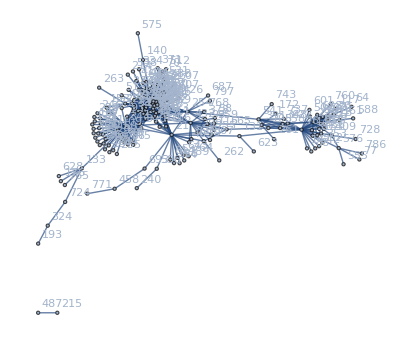

```mathematica
g2
```

## Load Network 2

### Node Research

```mathematica
Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]]
```

{47,157,170,398,741,718,299,27,348,394,665,548,541,743,578,535,558,775,408,271,327,60,612,587,534,486,670,441,236,176,648,72,622,458,432,392,366,254,108,380,164,531,281,192,526,795,738,465,378,307,261,240,233,172,90,581,346,301,21,756,18,796,518,470,468,343,707,259,235,410,171,406,363,193,700,596,562,403,262,206,479,138,135,112,659,788,777,689,636,542,537,418,321,309,280,194,161,116,56,215,782,749,713,607,564,620,798,771,400,699,662,630,340,330,504,325,316,693,292,460,249,247,228,227,211,205,190,364,272,641,623,263,168,716,711,668,601,317,305,270,255,183,140,120,100,84,304,75,131,64,51,792,753,737,728,727,723,705,690,638,627,625,613,603,595,577,576,573,566,530,515,491,483,481,473,434,401,391,368,354,349,337,312,296,295,277,276,268,239,213,202,195,189,149,126,117,115,113,104,102,97,79,78,61,58,54,49,105,347,50,3}

```mathematica
HighlightGraph[NeighborhoodGraph[g2,271,VertexLabels->"Name"],VertexList[g3]]
```

### Export Graph

```mathematica
Export[home<>prefix<>"net2_el"<>suffix<>".txt",EdgeList[g2]]
```

/home/lichao/scratch/caltech/face/net2_el.txt

## Load Network 3

### read Edge List

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_03_02"<>suffix<>".txt"]
```

```mathematica
el3=LoadNetwork3[home<>prefix<>"net3_el_015_02"<>suffix<>".txt"]
```

{1<->816,3<->889,3<->965,23<->149,23<->553,23<->607,28<->60,28<->151,28<->189,28<->245,28<->585,28<->710,28<->777,28<->786,28<->861,28<->1004,39<->51,45<->65,55<->653,57<->554,60<->189,60<->245,60<->422,60<->446,60<->914,60<->982,60<->997,65<->553,65<->568,65<->607,65<->817,68<->961,74<->629,91<->235,91<->316,93<->453,100<->248,100<->451,100<->496,100<->709,102<->271,102<->810,102<->910,104<->208,104<->613,104<->746,104<->884,117<->320,117<->624,117<->629,117<->635,118<->162,118<->785,118<->923,130<->517,133<->762,147<->643,149<->553,149<->607,151<->637,151<->670,151<->710,151<->746,151<->751,151<->785,151<->847,151<->861,151<->982,161<->294,161<->888,161<->938,161<->960,162<->637,162<->785,162<->923,189<->245,189<->585,189<->710,189<->982,190<->793,192<->673,200<->580,200<->822,208<->314,208<->512,208<->523,208<->541,208<->670,208<->744,208<->746,208<->785,208<->847,223<->387,223<->605,223<->726,225<->555,227<->338,227<->693,228<->263,228<->453,235<->284,245<->422,245<->585,245<->982,248<->709,261<->404,261<->735,263<->348,263<->453,263<->653,263<->999,264<->629,276<->653,283<->553,284<->488,284<->815,291<->888,294<->888,299<->594,299<->800,302<->946,313<->314,313<->354,313<->418,313<->517,313<->541,313<->693,313<->751,313<->787,313<->847,313<->947,313<->954,313<->968,314<->517,314<->541,314<->689,314<->746,314<->751,314<->771,314<->783,314<->787,314<->798,314<->847,314<->861,326<->389,338<->418,338<->709,348<->352,354<->512,354<->541,354<->693,354<->744,354<->783,354<->847,354<->954,362<->841,387<->649,387<->735,387<->919,404<->605,404<->735,408<->910,418<->517,418<->954,422<->585,422<->690,435<->649,435<->701,435<->946,439<->625,439<->680,446<->585,446<->914,446<->997,451<->496,451<->512,465<->764,465<->869,484<->568,489<->771,496<->512,496<->968,496<->969,510<->944,512<->523,512<->744,517<->689,517<->787,517<->844,517<->968,518<->741,518<->965,523<->670,523<->744,523<->783,538<->613,538<->785,538<->923,541<->693,541<->783,541<->847,541<->947,543<->726,553<->607,553<->764,555<->741,556<->696,556<->872,556<->1003,557<->559,568<->615,568<->817,578<->602,583<->888,585<->777,585<->785,585<->786,601<->609,604<->960,605<->701,605<->839,613<->887,613<->923,615<->811,625<->680,637<->689,637<->746,637<->751,637<->771,637<->785,637<->811,637<->861,637<->923,649<->946,670<->744,670<->847,688<->935,689<->771,689<->785,689<->798,689<->844,689<->861,693<->709,693<->954,702<->935,707<->987,710<->751,710<->777,710<->982,726<->839,744<->847,746<->771,746<->783,746<->785,746<->804,746<->847,751<->787,751<->847,751<->861,771<->798,771<->861,771<->968,777<->786,783<->847,785<->923,787<->847,804<->968,806<->922,828<->919,844<->890,847<->982,869<->886,869<->960,889<->965,895<->982,901<->918,935<->997,968<->969,996<->999}

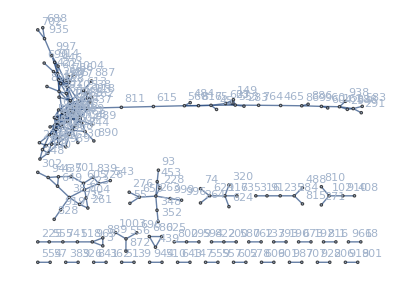

```mathematica
g3=Graph[el3,VertexLabels->"Name"]
```

```mathematica
VertexList[g3]//Sort//Length
EdgeList[g3]//Length
```

88

71

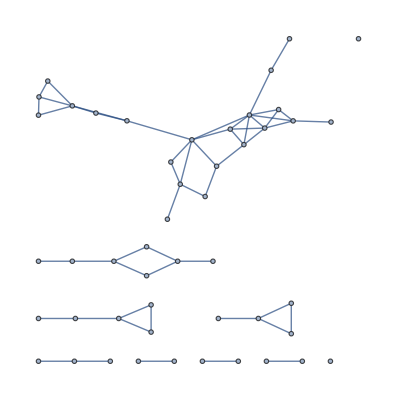

```mathematica
newg3=Subgraph[g3,newg2]
```

```mathematica
comp3=ConnectedComponents[Graph[el3]]
```

{{895,982,151,245,670,710,786,751,861,60,422,208,744,847,777,585,314,689,313,690,104,512,523,354,541,746,1004,517,637,771,783,787,798,844,693,954,841,451,496,785,902,130,418,615,811,968,890,709,362,100,804,969,538,923,338,248,503,561,613,162,227,207,913,921,794,887,724,178},{262,513,685,822,190,707,152,560,987,107,433,827,896,748,573,914,997,446,762},{29,10,137,263,228,348,453,653,93,352,520,35},{688,204,702,935,302,978,946,435,649,504,735,986},{320,117,458,128,624,629,635,98,74,264},{465,764,553,65,568,399,869,45,886},{889,3,161,965,938,960,518},{673,192,163,683},{57,223,554,53},{146,609,601},{604,643,888},{149,23,607},{225,25,555},{510,570,944},{701,605},{7,487},{368,188},{284,488},{115,389},{680,625},{46,145},{602,578},{577,729},{175,475},{580,200}}

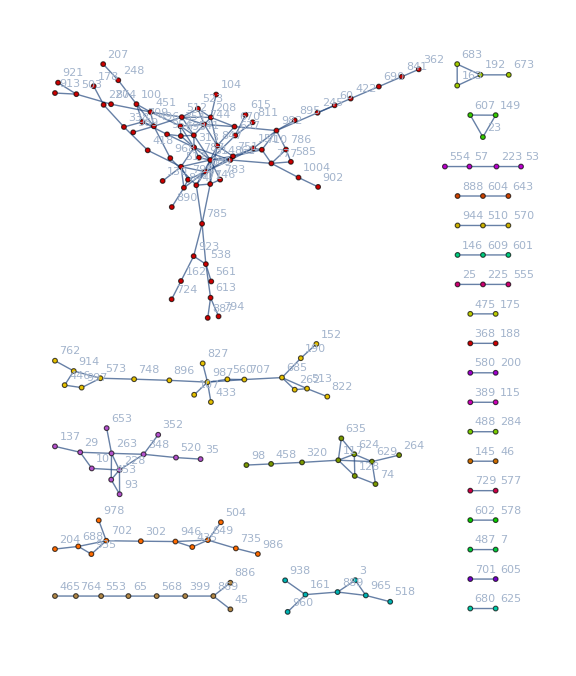

```mathematica
HighlightGraph[g3,comp3,ImageSize->Large]
```

```mathematica
Export[home<>prefix<>"net3_plot"<>suffix<>".pdf",%]
```

/home/lichao/scratch/pami/single_airplane/net3_plot_64.pdf

```mathematica
comp3=FindGraphCommunities[Graph[el3]]
```

{{151,861,104,208,613,746,884,118,162,785,923,637,670,751,847,314,512,523,541,744,313,354,787,947,689,771,783,798,489,538,887},{28,60,189,245,585,710,777,786,1004,422,446,914,982,997,690,688,935,702,895},{100,248,451,496,709,130,517,227,338,693,418,954,968,969,844,804,890},{223,387,605,726,261,404,735,302,946,649,919,435,701,543,839,828},{23,149,553,607,45,65,568,817,283,484,615,811},{161,294,888,938,960,291,465,764,869,583,604,886},{55,653,93,453,228,263,348,999,276,352,996},{3,889,965,225,555,518,741},{74,629,117,320,624,635,264},{91,235,316,284,488,815},{102,271,810,910,408},{556,696,872,1003},{200,580,822},{299,594,800},{439,625,680},{1,816},{39,51},{57,554},{68,961},{133,762},{147,643},{190,793},{192,673},{326,389},{362,841},{510,944},{557,559},{578,602},{601,609},{707,987},{806,922},{901,918}}

```mathematica
comp3=FindGraphCommunities[newg3]
```

{{105,268,626,736,612,501,304,744,763},{43,106,107,193,477,671,717},{79,311,72,95,239,485},{139,294,298,368,487,536},{382,546,742,630,591},{792,576,507,100},{160,187,140},{328,480},{555,728},{35,260},{16},{434}}

## Relation between net2 and net3

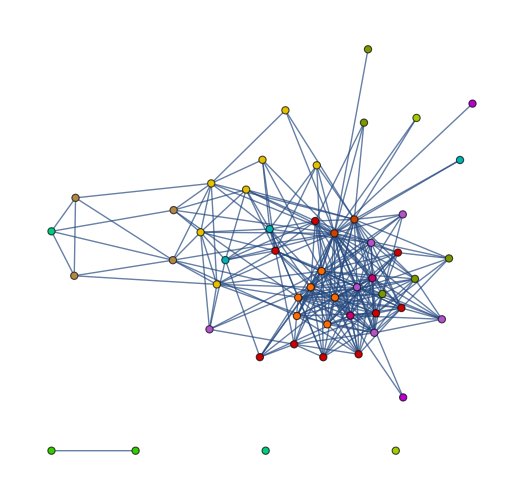

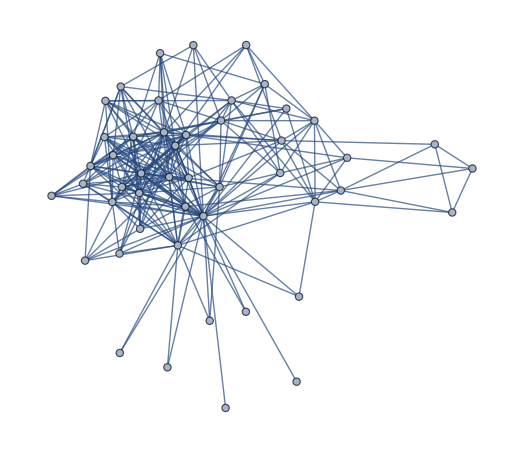

```mathematica
interGraph = Subgraph[g2,VertexList[g3]];
HighlightGraph[interGraph,comp3]
newg2= Subgraph[g2,ConnectedComponents[interGraph][[1]]]
```

```mathematica
VertexCount[newg2]
EdgeCount[newg2]
```

48

262

## Load Global data

```mathematica
{gx,gy,gs,gn}=LoadGlobalData[home<>prefix<>"converge_x"<>suffix<>".txt",home<>prefix<>"converge_y"<>suffix<>".txt",home<>prefix<>"converge_s"<>suffix<>".txt",home<>prefix<>"converge_n"<>suffix<>".txt"];
cx = gx+gs/2;cy=-(gy+gs/2);
```

```mathematica
cx;
```

```mathematica
Export[home<>prefix<>"global_summary"<>suffix<>".txt",Map[{#,gx[#],gy[#],gs[#]}&,Keys[gx]]]
```

Y:/vault/pami/next/single_airplane/global_summary.txt

```mathematica
Intersection[#,Keys[gx]]&/@comp3
```

{{31,58,59,245,292,559,638},{15,55,180,206,430,695},{7,43,120,374,722},{89,395,652},{33,62},{133,482},{136,333},{456,745},{641,733}}

```mathematica
Select[comp3,Length[#]>2&]
```

{{895,982,151,245,670,710,786,751,861,60,422,208,744,847,777,585,314,689,313,690,104,512,523,354,541,746,1004,517,637,771,783,787,798,844,693,954,841,451,496,785,902,130,418,615,811,968,890,709,362,100,804,969,538,923,338,248,503,561,613,162,227,207,913,921,794,887,724,178},{262,513,685,822,190,707,152,560,987,107,433,827,896,748,573,914,997,446,762},{29,10,137,263,228,348,453,653,93,352,520,35},{688,204,702,935,302,978,946,435,649,504,735,986},{320,117,458,128,624,629,635,98,74,264},{465,764,553,65,568,399,869,45,886},{889,3,161,965,938,960,518},{673,192,163,683},{57,223,554,53},{146,609,601},{604,643,888},{149,23,607},{225,25,555},{510,570,944}}

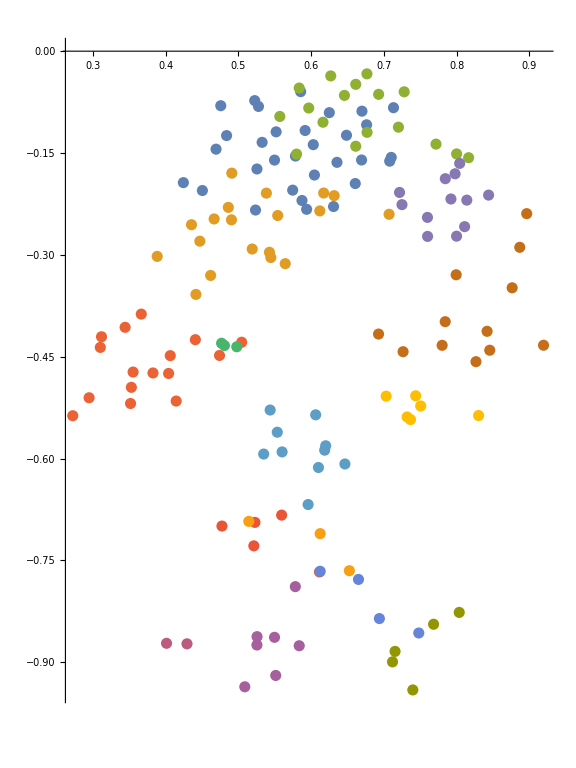

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,Select[comp3,Length[#]>2&],{2}],PlotRange->All,AspectRatio->4/3,ImageSize->Large]
```

```mathematica
ListPlot[Map[{cx[#],cy[#]}&,comp3,{2}],PlotRange->All,AspectRatio->4/3]
```

```mathematica
Mean/@Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{0.360756,0.344439,0.362133,0.38136,0.352032,0.396469,0.767527,0.3965,0.372281,0.330848,0.836027,0.366872,0.475844,0.335979,0.410927,0.412599,0.766951,0.674244}

```mathematica
Map[gs[#]&,Intersection[#,Keys[gx]]&/@comp3,{2}]
```

{{0.354006,0.361811,0.358521,0.341208,0.368141,0.380846},{0.330545,0.34774,0.342344,0.362643,0.338923},{0.374262,0.34284,0.363975,0.367456},{0.381039,0.389704,0.373338},{0.346285,0.357779},{0.39348,0.399458},{0.813928,0.721127},{0.38905,0.403949},{0.376815,0.367747},{0.334944,0.326751},{0.755648,0.916406},{0.370876,0.362867},{0.456433,0.495254},{0.333575,0.338383},{0.412666,0.409188},{0.407534,0.417664},{0.837074,0.696827},{0.785451,0.563036}}

```mathematica
sOrderByD = gs[#]&/@Part[VertexList[g2],Ordering[DegreeCentrality[g2],All,Greater]];
```

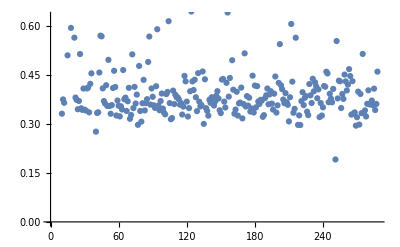

```mathematica
ListPlot[sOrderByD]
```

```mathematica
sOrderByP = gs[#]&/@Part[VertexList[g2],Ordering[PageRankCentrality[g2,0.1],All,Greater]];
```

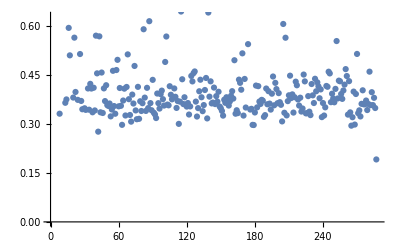

```mathematica
ListPlot[sOrderByP]
```

## Scale Slice

```mathematica
sLayers =SLayer[Keys[gx],gs]
```

<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>

```mathematica
ListPointPlot3D[Map[{cx[#],cy[#],gs[#]}&,Keys[gx]],Filling->Bottom,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}]
```

{{93,119,211,242},{47,83,144,278,299},{130,148,376},{62,99},{292},{15,129},{238},{55,118}}

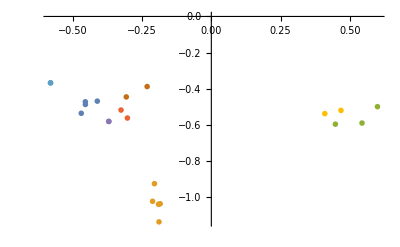

```mathematica
Module[{pos,idx},idx=DeleteCases[Intersection[#,sLayers[4]]&/@comp3,{}];pos=Map[{cx[#],cy[#]}&,idx,{2}];ListPlot[pos,PlotMarkers->idx]]
```

```mathematica
Export["ScaleLayer_"<>ToString[#]<>".pdf",SLayerPlot[#,sLayers,cx,cy]]&/@Keys[sLayers]
```

{ScaleLayer_6.pdf,ScaleLayer_5.pdf,ScaleLayer_4.pdf,ScaleLayer_3.pdf,ScaleLayer_8.pdf,ScaleLayer_9.pdf,ScaleLayer_7.pdf,ScaleLayer_1.pdf,ScaleLayer_10.pdf}

```mathematica
Directory
```

Directory

```mathematica
gall = Association[Map[#->{cx[#],cy[#],gs[#]}&,Keys[gx]]];
```

```mathematica
gall[0]
```

{0.111907,0.762903,0.476548}

```mathematica
SLayerPlot[1,sLayers,cx,cy]
```

SLayerPlot[1,<|6→{0,9,12,33,51,80,84,86,111,117,140,141,198,225,255,261,271,320,345,351,370},5→{2,7,14,20,22,23,31,35,36,37,40,49,54,57,61,63,64,66,69,77,82,85,89,90,94,103,112,121,124,126,136,138,139,142,145,153,154,158,160,161,163,165,166,167,169,171,174,176,177,179,184,187,191,193,195,197,199,202,203,204,206,208,209,213,216,222,224,227,234,236,243,246,252,256,257,263,267,269,281,283,284,285,291,293,295,296,297,298,300,301,302,304,306,307,309,313,318,322,327,330,334,335,338,340,352,354,361,364,365,368},4→{3,4,6,10,15,16,18,19,21,28,29,30,32,34,38,41,42,43,45,46,47,48,53,55,60,62,65,68,71,73,74,75,76,78,83,88,93,96,97,98,99,100,102,105,106,109,110,115,116,118,119,122,129,130,132,144,146,147,148,149,155,156,162,173,175,178,180,182,186,188,196,201,205,207,211,214,215,228,230,231,233,235,237,238,240,242,247,249,254,258,270,274,275,278,286,287,289,292,294,299,305,314,316,319,323,325,332,333,336,342,343,347,349,359,369,376},3→{5,24,52,67,92,107,133},8→{26,168,251,268,288,378,379,380,385},9→{56,72,128,135,328,344,356},7→{59,79,137,150,157,210,217,220,241,260,262,273,312,315,389},1→{218},10→{250,346}|>,cx,cy]

```mathematica
Manipulate[SLayerPlot[x,sLayers,cx,cy],{x,1,10,1}]
```

## Voronoi Centers for part

```mathematica
defined =Keys[gx];
```

```mathematica
voroComms= Intersection[defined,#]&/@Select[comp3,Length[#]>1&]
```

{{105,268,304,501,612,626,736,744,763},{43,106,107,193,477,671,717},{72,79,95,239,311,485},{139,294,298,368,487,536},{382,546,591,630,742},{100,507,576,792},{140,160,187},{328,480},{555,728},{35,260}}

```mathematica
centers =Mean/@Map[{gx[#],gy[#],Log[gs[#]]}&,voroComms,{2}]
```

{{-1.40882,-0.576347,-0.491948},{0.340279,-0.102082,-0.644462},{-1.55045,-0.321519,-0.538169},{-1.02274,-0.216805,-0.576281},{-1.20517,0.14597,-0.321124},{1.37332,-0.035153,-0.184234},{0.220983,0.120185,-0.790067},{-1.81625,-0.392541,0.120573},{-1.85442,-0.6238,-0.276838},{-0.958424,0.32075,-0.49529}}

```mathematica
ListPointPlot3D[centers]
```

-Graphics3D-

```mathematica
Length[centers]
```

10

```mathematica
Export[home<>prefix<>"voro_centers"<>suffix<>".txt",centers]
```

Y:/vault/pami/next/single_airplane/voro_centers.txt